```mathematica
data = Import["/home/cbapka/MEGA/Dropbox/Irish/Magnets_3.0/CPP/Flat_coil_modes/emf.dat","Data"];
```

```mathematica
model=(f+g*x+h*x^2+i*x^3 + j*x^5)/( a+b*x + c*x^2 + d*x^3 + e*x^4 )
```

(f+g x+h x^2+i x^3+j x^5)/(a+b x+c x^2+d x^3+e x^4)

```mathematica
fit = FindFit[data,model,{a,b, c,d,e,f,g,h,i,j},x,MaxIterations->250000]
```

{a→4.48382,b→-8473.45,c→6.60468×10^6,d→-2.53084×10^9,e→3.93247×10^11,f→-0.854092,g→1150.93,h→-483436.,i→6.22487×10^7,j→-3.82245×10^11}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},(-0.854092+1150.93 x-483436. x^2+6.22487×10^7 x^3-3.82245×10^11 x^5)/(4.48382-8473.45 x+6.60468×10^6 x^2-2.53084×10^9 x^3+3.93247×10^11 x^4)]

```mathematica
func1[z_]:=-287.3081201368885+721237.8199818128*(z)-7.933384389830811*10^8*z^2+4.980186190109384*10^11*z^3-1.9488231667351844*10^14*z^4+4.8644226666230424*10^16*z^5-7.560515532157858*10^18*z^6+6.688351807224581*10^20*z^7-2.578102130059701*10^22*z^8;
```

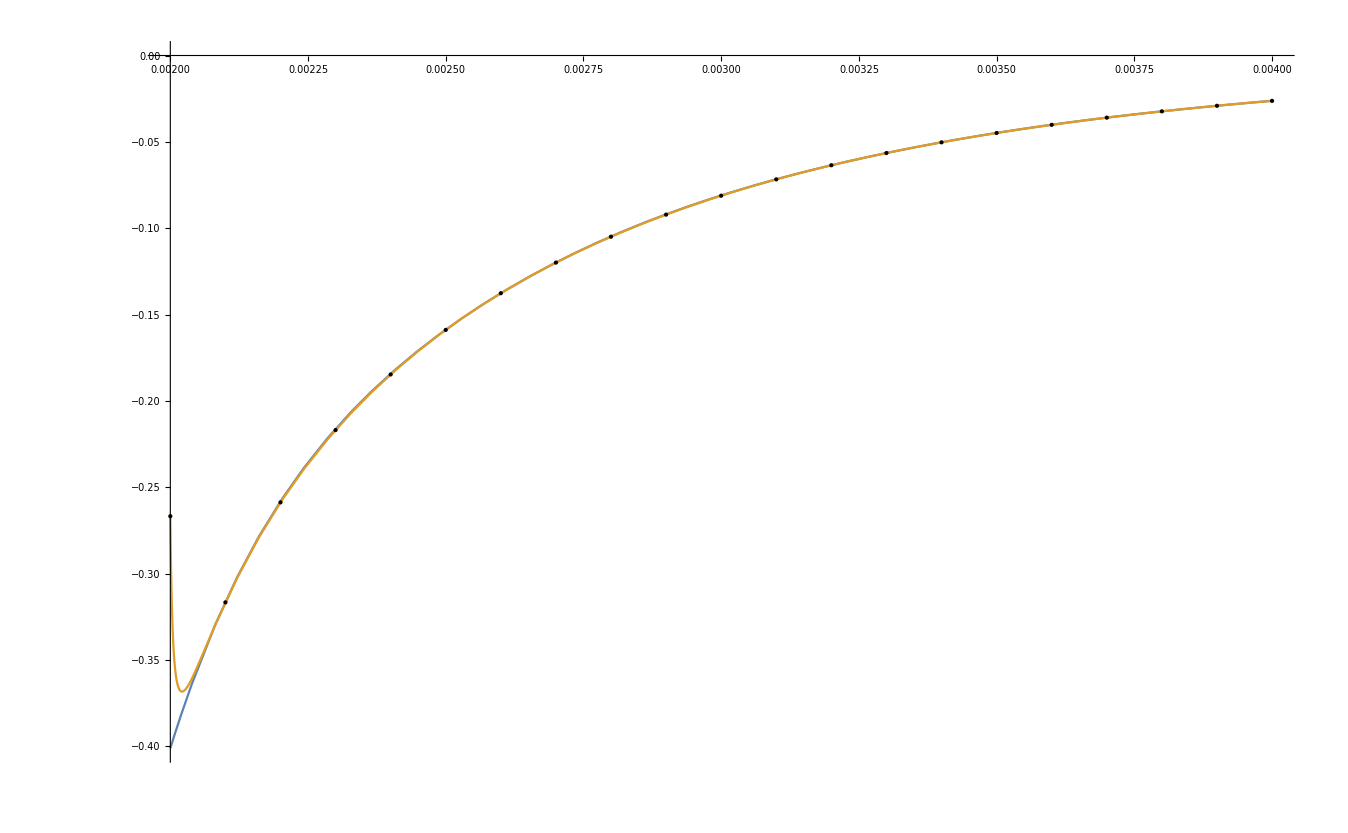

```mathematica
Plot[{func1[x],modelf[x]},{x,0.002,0.004},Epilog->Map[Point,data]]
```

```mathematica
CForm[(-0.8540921267394467+1150.9278844217931 x-483435.9688260379 x^2+6.2248686795744255*^7 x^3-3.8224484114907404*^11 x^5)/(4.4838175041083-8473.454048648566 x+6.604677180107996*^6 x^2-2.5308414452052097*^9 x^3+3.93246741422158*^11 x^4)]
```

(-0.8540921267394467 + 1150.9278844217931*x - 483435.9688260379*Power(x,2) + 6.2248686795744255e7*Power(x,3) - 3.8224484114907404e11*Power(x,5))/
   (4.4838175041083 - 8473.454048648566*x + 6.604677180107996e6*Power(x,2) - 2.5308414452052097e9*Power(x,3) + 3.93246741422158e11*Power(x,4))

```mathematica
data = Import["/home/cbapka/MEGA/Dropbox/Irish/Magnets_3.0/CPP/Flat_coil_modes/force_rot.dat","Data"];
```

```mathematica
model= a + b*x^2 + c*x^4 + d*x^6 + e* x^8
```

a+b x^2+c x^4+d x^6+e x^8

```mathematica
fit = FindFit[data,model,{a,b, c,d,e,f,g},x,MaxIterations->250000]
```

{a→-1.91341×10^-21,b→-7.54392×10^-11,c→-1.18697×10^-9,d→1.36719×10^-9,e→-4.50512×10^-7,f→0.,g→0.}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},-1.91341×10^-21-7.54392×10^-11 x^2-1.18697×10^-9 x^4+1.36719×10^-9 x^6-4.50512×10^-7 x^8]

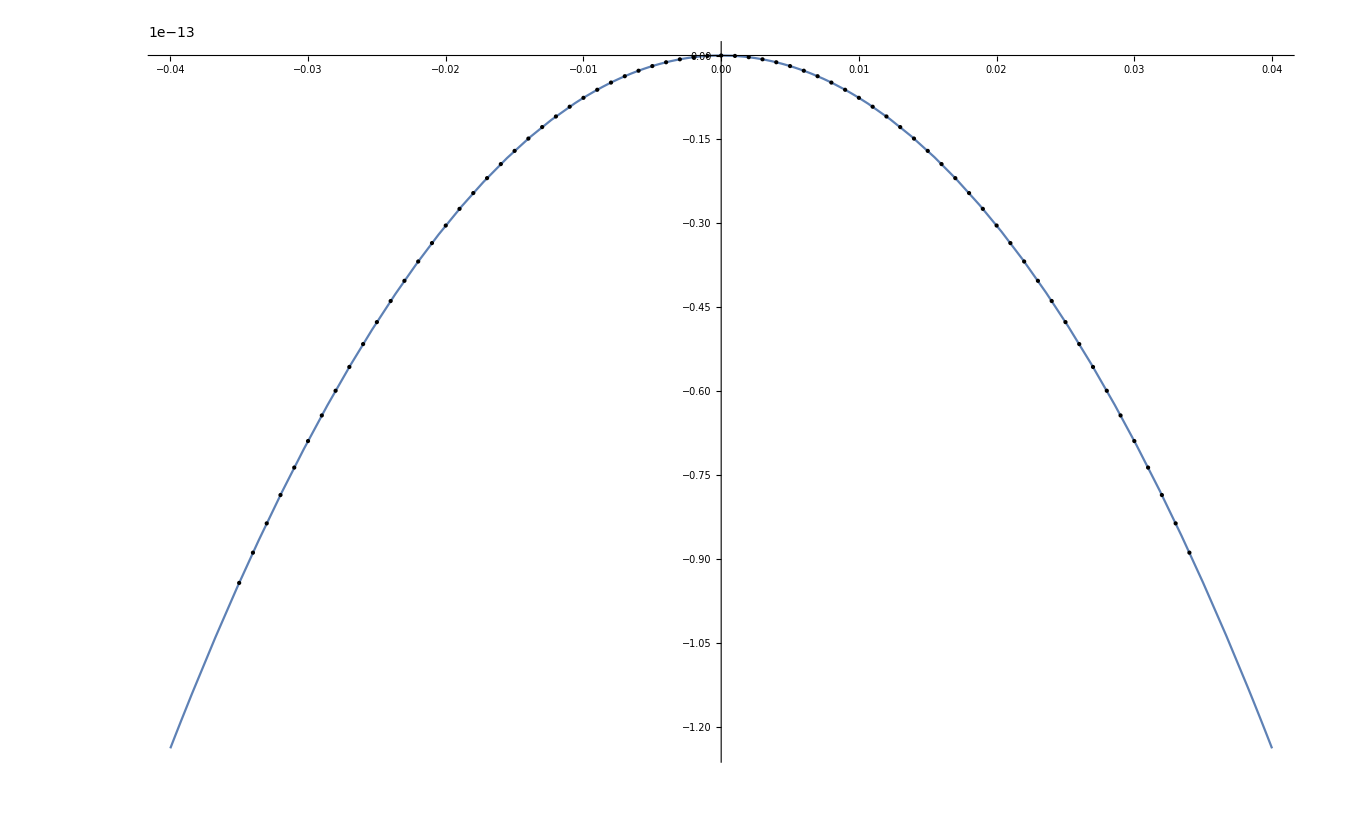

```mathematica
Plot[modelf[x],{x,-0.04,0.04},Epilog->Map[Point,data]]
```

```mathematica
CForm[-1.8461832348701756*^-17-7.541357584924355*^-11 x^2-1.1921442114522662*^-9 x^4+8.700445322549457*^-10 x^6+1.7777384605376496*^-8 x^8]
```

-1.8461832348701756e-17 - 7.541357584924355e-11*Power(x,2) - 1.1921442114522662e-9*Power(x,4) + 8.700445322549457e-10*Power(x,6) + 
   1.7777384605376496e-8*Power(x,8)

```mathematica
data = Import["/home/cbapka/MEGA/Dropbox/Irish/Magnets_3.0/CPP/Flat_coil_modes/force_perspect.dat","Data"];
```

```mathematica
model= (a + b*x  + c*x^2 + d*x^3 + e* x^4+f*x^5 + g*x^6 + h*x^7 + k*x^8)
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+k x^8

```mathematica
fit = FindFit[data,model,{a,b, c,d,e,f,g,h,k,l,m},x,MaxIterations->250000]
```

{a→-1.64887,b→4225.87,c→-4.73399×10^6,d→3.02422×10^9,e→-1.20412×10^12,f→3.05832×10^14,g→-4.83735×10^16,h→4.35542×10^18,k→-1.70885×10^20,l→0.,m→0.}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},-1.64887+4225.87 x-4.73399×10^6 x^2+3.02422×10^9 x^3-1.20412×10^12 x^4+3.05832×10^14 x^5-4.83735×10^16 x^6+4.35542×10^18 x^7-1.70885×10^20 x^8]

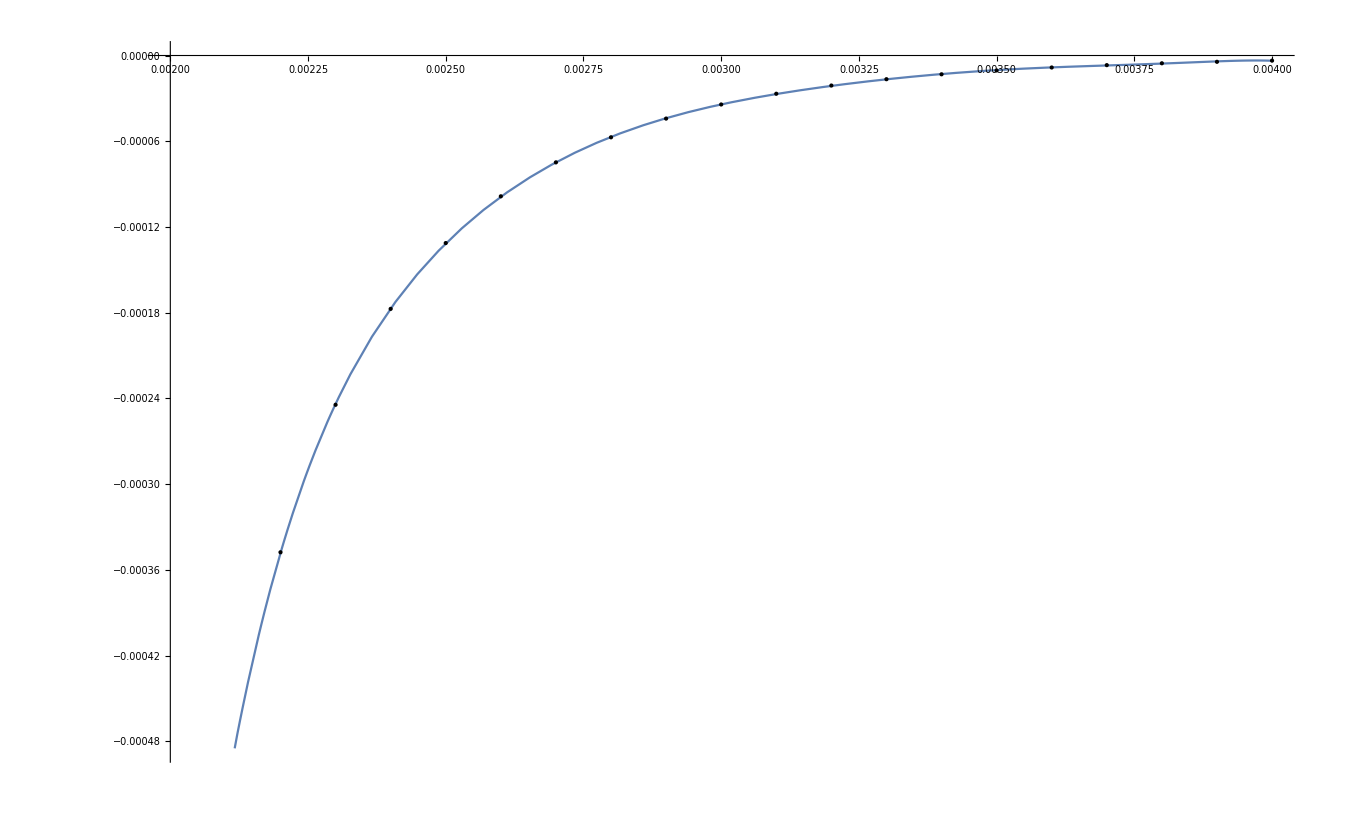

```mathematica
Plot[modelf[x],{x,0.002,0.004},Epilog->Map[Point,data]]
```